## Chapter 20

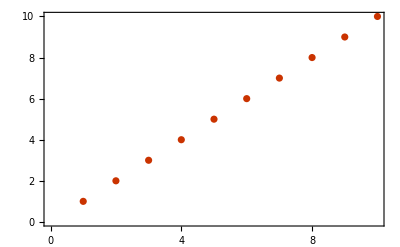

```mathematica
ListPlot[Range[10], PlotTheme -> "Web"]
```

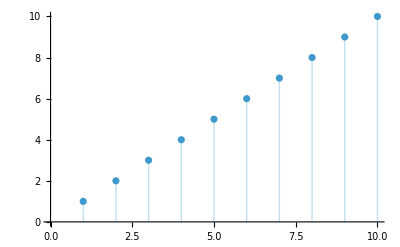

```mathematica
ListPlot[Range[10], Filling -> Axis]
```

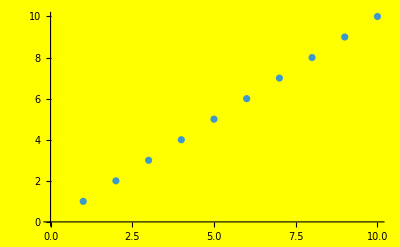

```mathematica
ListPlot[Range[10], Background -> Yellow]
```

```mathematica
GeoListPlot[Entity["Country", "Australia"], GeoRange -> All]
```

-Graphics-

```mathematica
GeoListPlot[Entity["Country", "Madagascar"], 
 GeoRange -> Entity["Ocean", "IndianOcean"]]
```

-Graphics-

```mathematica
GeoGraphics[EntityClass["Country", "SouthAmerica"], 
 GeoBackground -> "ReliefMap"]
```

-Graphics-

```mathematica
GeoListPlot[{Entity["Country", "France"], 
  Entity["Country", "Finland"], Entity["Country", "Greece"]}, 
 GeoLabels -> Automatic]
```

-Graphics-

```mathematica
GeoListPlot[EntityClass["University", "TheIvyLeague"], 
 GeoLabels -> Automatic]
```

-Graphics-

```mathematica
Grid[Table[Style[i j, RGBColor[1, 1, 1]], {i, 1, 12}, {j, 1, 12}], 
 Background -> Black]
```

1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12
2 | 4 | 6 | 8 | 10 | 12 | 14 | 16 | 18 | 20 | 22 | 24
3 | 6 | 9 | 12 | 15 | 18 | 21 | 24 | 27 | 30 | 33 | 36
4 | 8 | 12 | 16 | 20 | 24 | 28 | 32 | 36 | 40 | 44 | 48
5 | 10 | 15 | 20 | 25 | 30 | 35 | 40 | 45 | 50 | 55 | 60
6 | 12 | 18 | 24 | 30 | 36 | 42 | 48 | 54 | 60 | 66 | 72
7 | 14 | 21 | 28 | 35 | 42 | 49 | 56 | 63 | 70 | 77 | 84
8 | 16 | 24 | 32 | 40 | 48 | 56 | 64 | 72 | 80 | 88 | 96
9 | 18 | 27 | 36 | 45 | 54 | 63 | 72 | 81 | 90 | 99 | 108
10 | 20 | 30 | 40 | 50 | 60 | 70 | 80 | 90 | 100 | 110 | 120
11 | 22 | 33 | 44 | 55 | 66 | 77 | 88 | 99 | 110 | 121 | 132
12 | 24 | 36 | 48 | 60 | 72 | 84 | 96 | 108 | 120 | 132 | 144


{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Graphics[Disk[], ImageSize -> RandomInteger[40]], 100]
```

```mathematica
Table[Graphics[RegularPolygon[5], ImageSize -> 30, 
  AspectRatio -> n], {n, 1, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Manipulate[Graphics[Circle[], ImageSize -> n], {n, 5, 500}]
```

```mathematica
Grid[Table[RandomColor[], 10, 10], Frame -> All]
```

RGBColor[0.384575960982934, 0.830218019051586, 0.7662076976795562] | RGBColor[0.5017568819758649, 0.9421308326733802, 0.7356480011864011] | RGBColor[0.19511681738537456, 0.8671975957400866, 0.41795640729172434] | RGBColor[0.2400124692965857, 0.2799072226408177, 0.2963444720233406] | RGBColor[0.3424169668105099, 0.7225771738738924, 0.45710149257788846] | RGBColor[0.08607789374488095, 0.27562117529914376, 0.2502792119728834] | RGBColor[0.534456597000027, 0.8980314723690035, 0.26974637877806584] | RGBColor[0.22761711875817459, 0.7820052754305944, 0.3281039639275789] | RGBColor[0.8779028173550689, 0.9994508775149364, 0.059543059436406365] | RGBColor[0.5914770886522109, 0.38807578441078516, 0.7686007613169357]
RGBColor[0.4754619241907432, 0.6276220705120255, 0.48089283523491355] | RGBColor[0.245656505866789, 0.7454957434789864, 0.5364578500152599] | RGBColor[0.6632481161322337, 0.9691283133971773, 0.13201812338004615] | RGBColor[0.1435644374327847, 0.8459957908389688, 0.18783466904821244] | RGBColor[0.20126069359743637, 0.253930581092517, 0.09052456843814793] | RGBColor[0.9465333934442661, 0.6604799493278626, 0.16654876988386746] | RGBColor[0.9681210484386069, 0.4231253724425017, 0.680446761544637] | RGBColor[0.6521979598375134, 0.9625757753997133, 0.1493768937219111] | RGBColor[0.5497226713504666, 0.45288126557865716, 0.5944133843084054] | RGBColor[0.8680028917677884, 0.94040566330575, 0.5961033061736722]
RGBColor[0.322025871980115, 0.7962153332306152, 0.2464102579612213] | RGBColor[0.28263624593252823, 0.1361617576082088, 0.6971598730704178] | RGBColor[0.8819757724471, 0.6112311379784596, 0.3334939779871249] | RGBColor[0.4079963391616086, 0.3826994223042379, 0.7281205958406818] | RGBColor[0.1467499997220889, 0.1103596771347124, 0.8107057820379555] | RGBColor[0.8998894377870232, 0.07041162527762634, 0.6452885823630046] | RGBColor[0.6220037437661412, 0.26592318020101136, 0.12460234793675862] | RGBColor[0.024199220670176214, 0.5925495177364257, 0.47812113883923035] | RGBColor[0.13553342035696092, 0.18693151086573256, 0.9974316537031462] | RGBColor[0.3563588174431873, 0.6721165996527829, 0.13088076992990438]
RGBColor[0.04753970829280307, 0.9721307204663325, 0.7185041600578026] | RGBColor[0.3916127107212066, 0.21228022729225193, 0.36487584828348996] | RGBColor[0.9571817559502505, 0.8698101450204627, 0.11676136994065511] | RGBColor[0.8670981364243251, 0.4223746819825125, 0.3632388365769432] | RGBColor[0.1900614404558103, 0.4402943433432229, 0.35305204975811355] | RGBColor[0.35383156323559484, 0.8759950099668992, 0.8743845909343373] | RGBColor[0.867460865818332, 0.821783419974667, 0.19812531429953917] | RGBColor[0.34190667333925284, 0.4798305378915617, 0.9187130537976644] | RGBColor[0.5924331768509339, 0.25044239013893077, 0.20543698660926202] | RGBColor[0.32137293812357526, 0.6145651936214787, 0.06294689230620198]
RGBColor[0.15939308642147965, 0.14315593775074875, 0.8994748041523501] | RGBColor[0.4756382862154611, 0.602362095238619, 0.8199127684921095] | RGBColor[0.8878593433401518, 0.8525236238688949, 0.4825028628415573] | RGBColor[0.8202908113190166, 0.34292957655171086, 0.32405380936571415] | RGBColor[0.1994913996254819, 0.36882441335240657, 0.7688874105844554] | RGBColor[0.3164082880281389, 0.03854784574709669, 0.27581046869341086] | RGBColor[0.8832902758166372, 0.6788708428541106, 0.8076620032382626] | RGBColor[0.5875976812653938, 0.24525584854866778, 0.6736643710974008] | RGBColor[0.06036042535465769, 0.12564953209979035, 0.5324896354024664] | RGBColor[0.3262598488796076, 0.3670235588021449, 0.45206472744047166]
RGBColor[0.61012522389049, 0.014119715617985307, 0.9672509708953407] | RGBColor[0.5155166921391152, 0.16946174508612755, 0.49850591827652124] | RGBColor[0.8516812834016245, 0.827768889364757, 0.829949768445428] | RGBColor[0.12717608794993662, 0.4939323093575039, 0.2106584997982488] | RGBColor[0.021753715732220513, 0.07028789170663763, 0.6422041317966349] | RGBColor[0.19892605188133183, 0.677232739896753, 0.4085808987590478] | RGBColor[0.3704834308187799, 0.9207540258719156, 0.11675157999598929] | RGBColor[0.46124103968761787, 0.8835956224358552, 0.8146403331298626] | RGBColor[0.13723367915736184, 0.7213804256597822, 0.4590951677099522] | RGBColor[0.37163839596219184, 0.3411404025232303, 0.9406210895243596]
RGBColor[0.5476057437868744, 0.07205425367977636, 0.4748688952548039] | RGBColor[0.943315139291037, 0.36070469341836175, 0.9165129152051157] | RGBColor[0.29779433997103033, 0.6558458483888385, 0.7872056512812491] | RGBColor[0.6454678472893236, 0.6756825632812988, 0.6187746701513841] | RGBColor[0.6868001373584298, 0.7703918096856031, 0.46024165816699236] | RGBColor[0.6812195551231617, 0.8390608786491411, 0.46032913423134936] | RGBColor[0.05801444004460876, 0.17043999511083707, 0.9178105960522045] | RGBColor[0.22213397304567484, 0.04385852036156712, 0.1086707741300994] | RGBColor[0.0498698848183845, 0.06901147167978783, 0.8810387203021048] | RGBColor[0.27870300163522654, 0.9722403684518905, 0.244640298966031]
RGBColor[0.21456514003383353, 0.609124810449374, 0.8389347385895625] | RGBColor[0.09349298895449265, 0.7017371675037329, 0.8706846206711187] | RGBColor[0.5300450920512008, 0.5609112560812788, 0.5412389066187391] | RGBColor[0.30412985290350614, 0.04544719527739738, 0.5022489767239371] | RGBColor[0.8668885718003625, 0.6243050606598133, 0.4384833554041194] | RGBColor[0.24701895805305862, 0.7399497226247376, 0.5570677749957726] | RGBColor[0.5095746341185288, 0.9802540292663646, 0.2089860593238777] | RGBColor[0.4654771382347864, 0.8183429902913426, 0.476912560615137] | RGBColor[0.09932959293577115, 0.7696400599364643, 0.279846821926256] | RGBColor[0.20905925124246538, 0.5210284838828609, 0.505306883065221]
RGBColor[0.03707643901126745, 0.32518715002247567, 0.7737293801094449] | RGBColor[0.5816542509008193, 0.3305811806542458, 0.4909739027921509] | RGBColor[0.9952407432795345, 0.9106172697626578, 0.31194106242401287] | RGBColor[0.9797769892888124, 0.49289781348701256, 0.3800672880106366] | RGBColor[0.1706843847161139, 0.35119412586432963, 0.3087940581092088] | RGBColor[0.4880495816988366, 0.9292576697847581, 0.9733658928734015] | RGBColor[0.2883854885855637, 0.5055776313971205, 0.7055478005939293] | RGBColor[0.5556269996076715, 0.3255744594477903, 0.8488015526051138] | RGBColor[0.5444450684418649, 0.2956753410412285, 0.7057013472524438] | RGBColor[0.10958633507523663, 0.664712902002589, 0.5243901219727429]
RGBColor[0.05977538378980474, 0.1733957356488378, 0.1004658012602273] | RGBColor[0.8133235323712829, 0.696572199354557, 0.4321757331867957] | RGBColor[0.16636004370293356, 0.9773090464466834, 0.7939620573666026] | RGBColor[0.7298647475244326, 0.1178990445254231, 0.8138743169190936] | RGBColor[0.5326545959888436, 0.2795128502588662, 0.6126512920004916] | RGBColor[0.009272664668299013, 0.350286414104634, 0.8553746964681457] | RGBColor[0.8211817319895989, 0.7934890264651755, 0.7875567828547112] | RGBColor[0.34261430810620075, 0.4589192927005752, 0.2391631835628174] | RGBColor[0.4265439109870526, 0.19342091029808084, 0.9774151512848095] | RGBColor[0.2296833955698594, 0.6927341692377167, 0.7281795806149356]

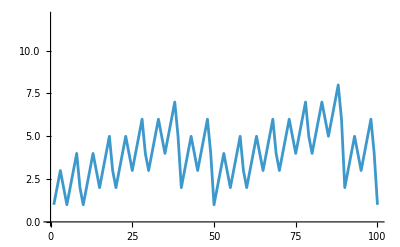

```mathematica
ListLinePlot[Table[Length[Characters[RomanNumeral[n]]], {n, 1, 100}], 
 PlotRange -> 
  Max[Table[Length[Characters[RomanNumeral[n]]], {n, 1000}]]]
```

## Chapter 21

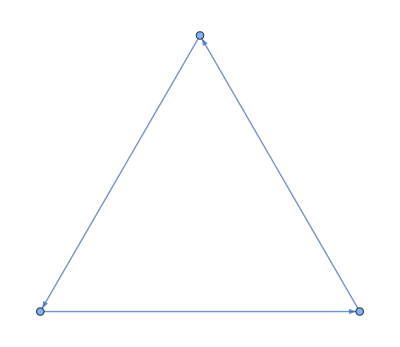

```mathematica
Graph[{1->2,2->3,3->1}]
```

```mathematica
Graph[Flatten[Table[i->j,{i,4},{j,4}]]]
```

-Graphics-

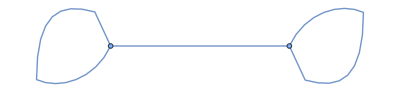
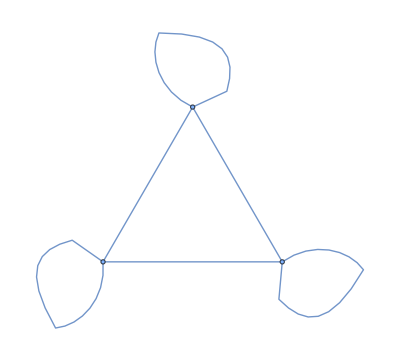
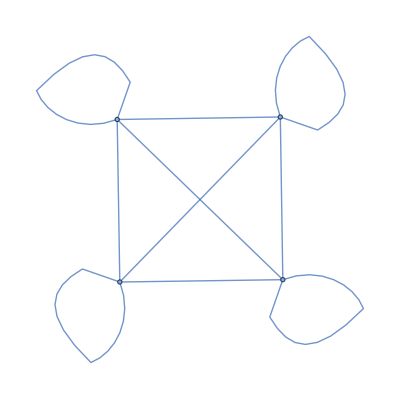
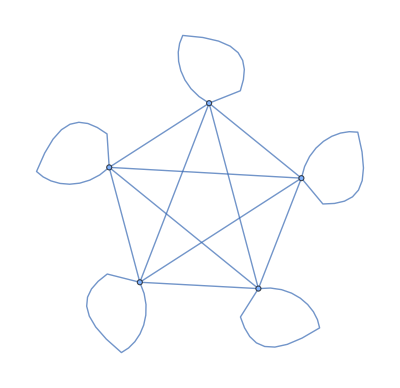
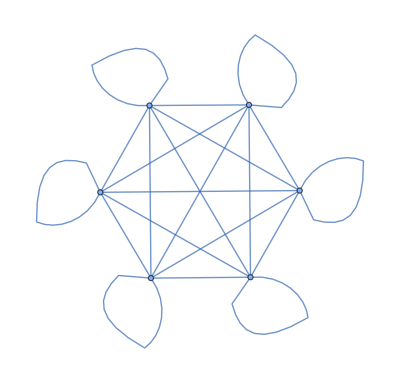
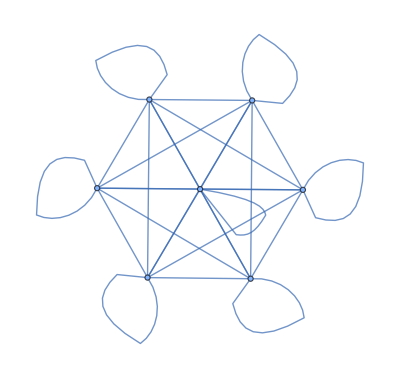
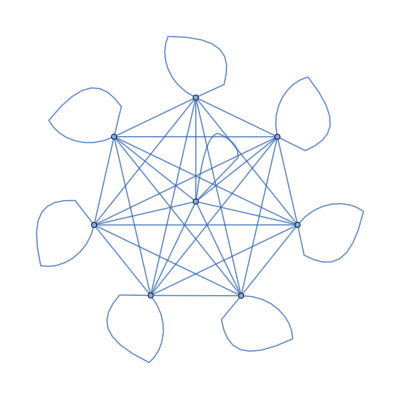
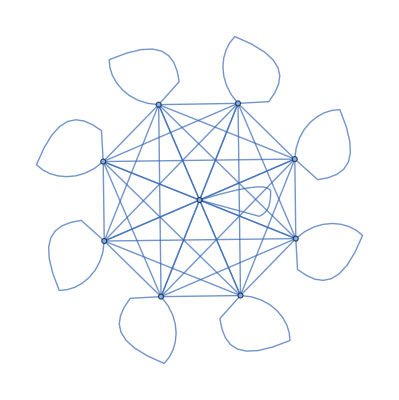

```mathematica
Table[UndirectedGraph[Flatten[Table[i->j,{i,n},{j,n}]]],{n,2,10}]
```

```mathematica
Flatten[Table[{1,2},3]]
```

{1,2,1,2,1,2}

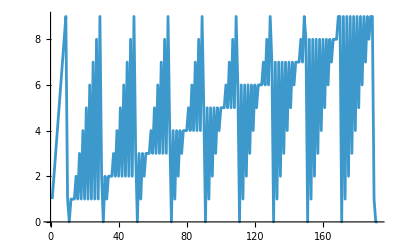

```mathematica
ListLinePlot[Flatten[IntegerDigits[Range[100]]]]
```

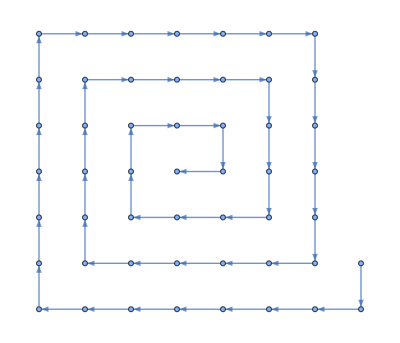

```mathematica
Graph[Flatten[Table[i->i+1,{i,50}]]]
```

```mathematica
Table[i->Max[i,j],j->Max[i,j],{i,4},{j,4}]
```

Table::nliter: Non-list iterator j→Max[i,j] at position 2 does not evaluate to a real numeric value.

Table[i→Max[i,j],j→Max[i,j],{i,4},{j,4}]

```mathematica
Graph[Flatten[Table[i->(j-i),j->(j-i),{i,1,5},{j,1,5}]]]
```

Table::nliter: Non-list iterator j→j-i at position 2 does not evaluate to a real numeric value.

Graph[Table[i→j-i,j→j-i,{i,1,5},{j,1,5}]]

```mathematica
Graph[Table[i->RandomInteger[100],{i,100}]]
```

-Graphics-

```mathematica
Grid[Table[FindShortestPath[Graph[{1->2, 2->3, 3->4, 4->1, 3->1, 2->2}],a,b],{a,4},{b,4}]]
```

{1} | {1,2} | {1,2,3} | {1,2,3,4}
{2,3,1} | {2} | {2,3} | {2,3,4}
{3,1} | {3,1,2} | {3} | {3,4}
{4,1} | {4,1,2} | {4,1,2,3} | {4}

# Chapter 22

```mathematica
LanguageIdentify["ajatella"]
```

Finnish

```mathematica
ImageIdentify[["Image"]]
```

tiger

```mathematica
Table[ImageIdentify[Blur[["Image"],n]],{n,5}]
```

{tiger,tiger,tiger,tiger,swift fox}

```mathematica
Classify["Sentiment","I'm so happy to be here"]
```

Positive

```mathematica
Nearest[WordList[],"happy",10]
```

{happy,haply,harpy,nappy,sappy,apply,campy,choppy,guppy,hairy}

```mathematica
Nearest[Table[RandomInteger[1000],20],1000,3]
```

{998,952,951}

```mathematica
Nearest[Table[RandomColor[],10],RGBColor[1,0,0],5]
```

{RGBColor[0.9114493622620004, 0.1267070210361796, 0.3062060679934795],RGBColor[0.660203402554, 0.32435968199962506, 0.25408008008084737],RGBColor[0.9067128011400796, 0.5662866577158652, 0.6693788226331172],RGBColor[0.7818922010727078, 0.05251018581269884, 0.6059079005040715],RGBColor[0.2163438083495448, 0.33327079723269937, 0.05971908603612852]}

```mathematica
Nearest[Table[n^2,{n,100}],2000]
```

{2025}

```mathematica
Nearest[EntityValue[Entity["GeographicRegion","Europe"][EntityProperty["GeographicRegion","Countries"]],"Flag"],["Flag"],3]
```

{-Graphics-,-Graphics-,-Graphics-}

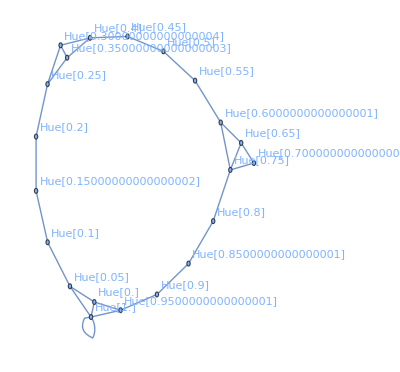

```mathematica
NearestNeighborGraph[Table[Hue[h], {h, 0, 1, .05}],2,VertexLabels->All]
```

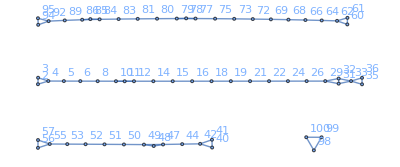

```mathematica
NearestNeighborGraph[Table[RandomInteger[100],100],2,VertexLabels->All]
```


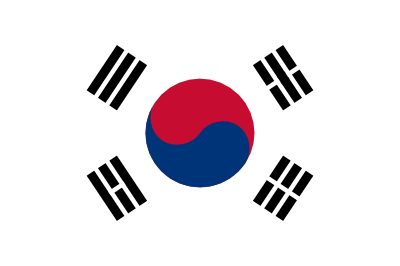
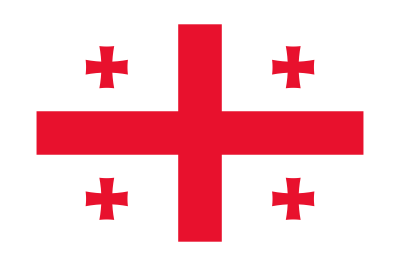
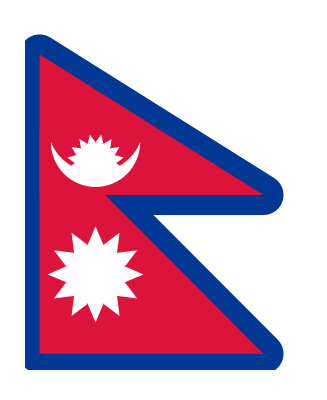
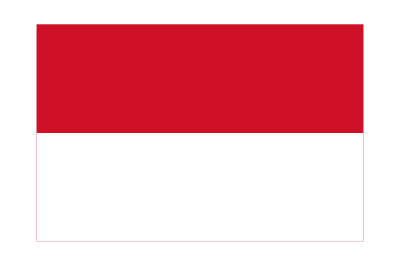
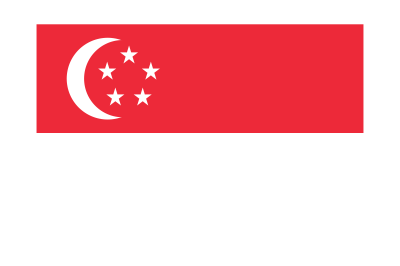
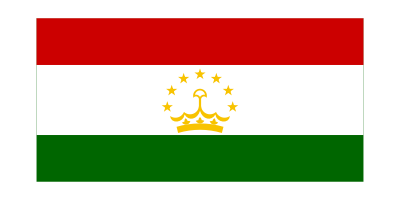
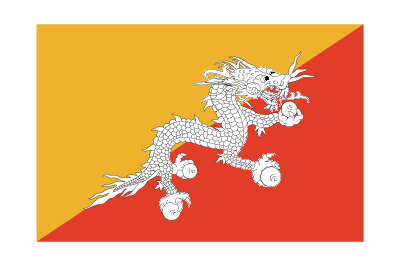
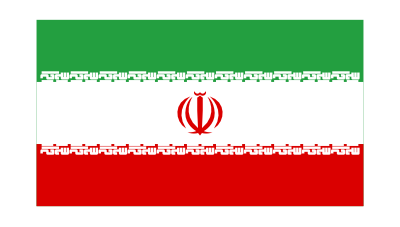

{{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-},{-Graphics-,-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
FindClusters[EntityValue[,"Flag"]]
```

```mathematica
NearestNeighborGraph[Table[Rasterize[Style[FromLetterNumber[n],20]],{n,26}],2,VertexLabels->All]
```

-Graphics-

```mathematica
Table[TextRecognize[EdgeDetect[Rasterize[Style["Programming ",n]]]],{n,1,10}]
```

{,,,,Programing,Pri
ogramming,Programming,Programming,Programming,Programming}

```mathematica
Dendrogram[Table[Rasterize[FromLetterNumber[n]],{n,10}]]
```

-Graphics-

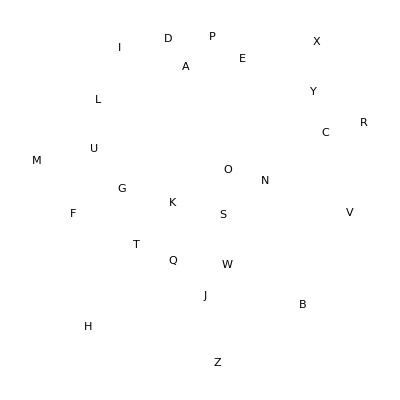

```mathematica
FeatureSpacePlot[Capitalize[Alphabet[]]]
```